```mathematica
SetDirectory["C:\\Users\\WizardOf\\Documents\\Visual Studio 2013\\Projects\\ParallelComputingHomework\\ex04"];
```

# Warning, all Plots are generated with local execution time, as we don’t have access to the cluster, so no real conclusions can be drawn

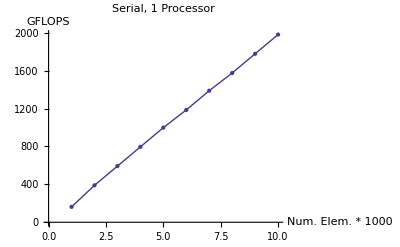

```mathematica
serialList=ToExpression/@(StringDrop[#, -1]&/@Import["ex01a_1.out", "Table"]⟦All, 2⟧);
ListPlot[serialList, Joined->True, Mesh->All, AxesLabel->{"Num. Elem. * 1000", "GFLOPS"}, PlotLabel->"Serial, 1 Processor"]
```

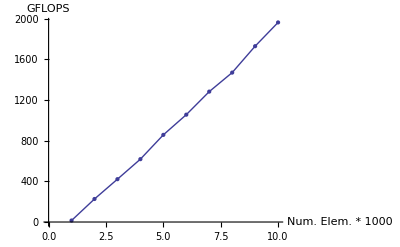
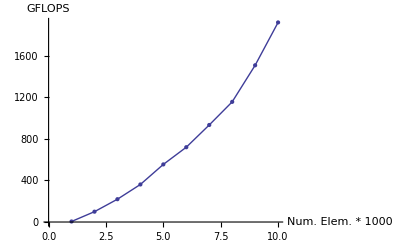
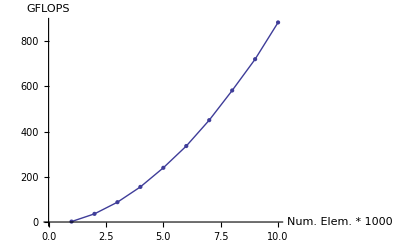
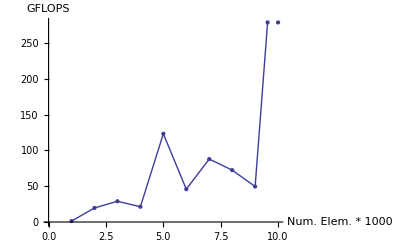
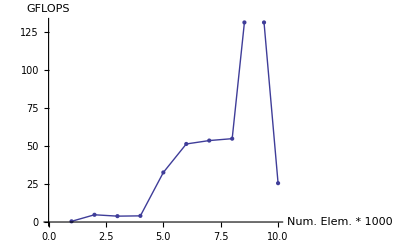
Number of Processors | 1 | 2 | 4 | 8 | 16
Rec. Doubl. Performance | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
perfBList=ListPlot[#, Joined->True, Mesh->All, AxesLabel->{"Num. Elem. * 1000", "GFLOPS"}]&/@ToExpression/@(StringDrop[#, -1]&/@Import["ex01b_"<>ToString[#]<>".out", "Table"]⟦All, 2⟧&)/@(2^(Range[5]-1));
Grid[{{"Number of Processors", "1", "2", "4", "8", "16"}, PrependTo[perfBList, "Rec. Doubl. Performance"]}, Frame->All]
```

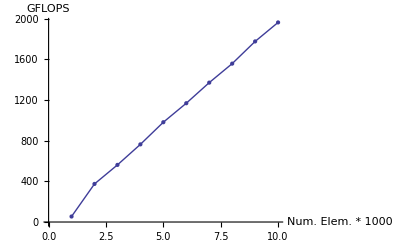
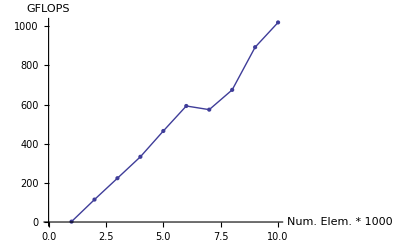
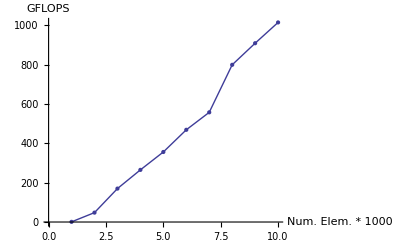
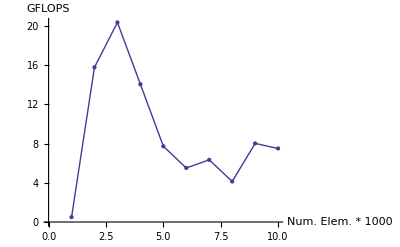
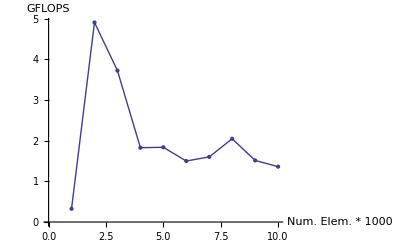
Number of Processors | 1 | 2 | 4 | 8 | 16
Butterfly Performance | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
perfCList=ListPlot[#, Joined->True, Mesh->All, AxesLabel->{"Num. Elem. * 1000", "GFLOPS"}]&/@ToExpression/@(StringDrop[#, -1]&/@Import["ex01c_"<>ToString[#]<>".out", "Table"]⟦All, 2⟧&)/@(2^(Range[5]-1));
Grid[{{"Number of Processors", "1", "2", "4", "8", "16"}, PrependTo[perfCList, "Butterfly Performance"]}, Frame->All]
```